```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=β∈Reals&&Ω∈Reals&&t∈Reals&&β>0 && Ω>0 &&t>0&&β<π/4&&ωL∈Reals&& ωL>0&&A∈Reals&&A>0&&B∈Reals&&B>0&& m∈PositiveIntegers&&k∈PositiveIntegers
```

β∈ℝ&&Ω∈ℝ&&t∈ℝ&&β>0&&Ω>0&&t>0&&β<π/4&&ωL∈ℝ&&ωL>0&&A∈ℝ&&A>0&&B∈ℝ&&B>0&&m∈ℤ&&m>0&&k∈ℤ&&k>0

```mathematica
Ucnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
```

```mathematica
(*first check should be if we get the correct dynamics with B=0 and with/without off-resonant drive*)
H0check=((ωL*Cos[β]-ω)*Cos[β])/2*PauliMatrix[3]+(-ω*Sin[β]+Ω0*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω0*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H1check=((ω1-ω)*Cos[β]+Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H0check //MatrixForm
H1check //MatrixForm
```

(A/2 | 1/2 Ω0 Cos[ϕ]-1/2 ⅈ Ω0 Sin[ϕ]
1/2 Ω0 Cos[ϕ]+1/2 ⅈ Ω0 Sin[ϕ] | -A/2)

(0 | 1/2 Ω Cos[ϕ]-1/2 ⅈ Ω Sin[ϕ]
1/2 Ω Cos[ϕ]+1/2 ⅈ Ω Sin[ϕ] | 0)

```mathematica
(*OK passt!!*)
```

```mathematica
(*now build time evolution operator including off-resonant driving and perpendicular component for both subspaces*)
```

```mathematica
(*Hamiltonian for both electronic subspaces in RF with RWA*)
```

```mathematica
H0=((ωL*Cos[β]-ω)*Cos[β])/2*PauliMatrix[3]+(-ω*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2];
H1=((ω1-ω)*Cos[β]+Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2];
```

```mathematica
H0 //MatrixForm
H1 //MatrixForm
```

(1/2 Cos[β] (-ω+ωL Cos[β]) | 1/2 (Ω Cos[β]^2 Cos[ϕ]-ω Sin[β])-1/2 ⅈ Ω Cos[β] Sin[ϕ]
1/2 (Ω Cos[β]^2 Cos[ϕ]-ω Sin[β])+1/2 ⅈ Ω Cos[β] Sin[ϕ] | -1/2 Cos[β] (-ω+ωL Cos[β]))

(1/2 ((-ω+ω1) Cos[β]+Ω Cos[β] Cos[ϕ] Sin[β]) | 1/2 (Ω Cos[β]^2 Cos[ϕ]+(-ω+ω1) Sin[β])-1/2 ⅈ Ω Cos[β] Sin[ϕ]
1/2 (Ω Cos[β]^2 Cos[ϕ]+(-ω+ω1) Sin[β])+1/2 ⅈ Ω Cos[β] Sin[ϕ] | 1/2 (-((-ω+ω1) Cos[β])-Ω Cos[β] Cos[ϕ] Sin[β]))

```mathematica
U0=MatrixExp[-ⅈ*H0*t];
U1 = MatrixExp[-ⅈ*H1*t];
```

```mathematica
(*I could not run this test because the evalution took too long:*)
Transpose[Conjugate[U0]].U0//ComplexExpand//Simplify//MatrixForm
```

```mathematica
Transpose[Conjugate[U1]].U1//ComplexExpand//Simplify//MatrixForm
```

```mathematica
(*first check sequence for a CNOT on nuclear spin without dynamical decoupling sequences*)
```

```mathematica
(*build time evolution operator, plug in condition for driving frequency ω and phase ϕ*)
H0s=H0/.{ϕ->0,ω->Ω*Sin[β]+ω1};
H1s=H1/.{ϕ->0,(ω1-ω)->-Ω*Sin[β]}//FullSimplify; 
H0s//MatrixForm
H1s//MatrixForm
```

(1/2 Cos[β] (-ω1+ωL Cos[β]-Ω Sin[β]) | 1/2 (Ω Cos[β]^2-Sin[β] (ω1+Ω Sin[β]))
1/2 (Ω Cos[β]^2-Sin[β] (ω1+Ω Sin[β])) | -1/2 Cos[β] (-ω1+ωL Cos[β]-Ω Sin[β]))

(0 | 1/2 Ω Cos[2 β]
1/2 Ω Cos[2 β] | 0)

```mathematica
U0s=MatrixExp[-ⅈ*H0s*t];
U1s = MatrixExp[-ⅈ*H1s*t]
```

{{Cos[1/2 t Ω Cos[2 β]],-ⅈ Sin[1/2 t Ω Cos[2 β]]},{-ⅈ Sin[1/2 t Ω Cos[2 β]],Cos[1/2 t Ω Cos[2 β]]}}

```mathematica
Transpose[Conjugate[U0s]].U0s//FullSimplify//MatrixForm
```

```mathematica
Transpose[Conjugate[U1s]].U1s//FullSimplify//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
(*Get condition for gate time for a NOT in the 1-subspace and plug it in the time evolution operator*)
```

```mathematica
Solve[U1s=={{0,-ⅈ},{-ⅈ,0}},t]
```

{{t→ConditionalExpression[((π+4 π C[1]) Sec[2 β])/Ω, C[1]∈ℤ&&C[1]≥0]}}

```mathematica
U0s=MatrixExp[-ⅈ*H0s*t]/.t->(π* Sec[2 β])/Ω;
U1s = MatrixExp[-ⅈ*H1s*t]/.t->(π* Sec[2 β])/Ω
```

{{0,-ⅈ},{-ⅈ,0}}

```mathematica
(*This is the analytically derived synchronization condition. I could not solve it for Omega when using the sine and cosine expressions for the perpedicular component of the hyperfine coupling. Thus I replace them here and solve for Omega*)
```

```mathematica
(((ωL*Cos[β]^2-Ω*Sin[β]*Cos[β]-ω1*Cos[β])^2+(Ω*(Cos[β]^2-Sin[β]^2)-ω1*Sin[β])^2)/(Ω*(Cos[β]^2-Sin[β]^2))^2)==(4*m^2)/k^2/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B^2/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2],m->1,k->1}
```

((A-ωL-(B^2 Ω (-A+ωL))/(B^2+(-A+ωL)^2)+(ωL (-A+ωL)^2)/(B^2+(-A+ωL)^2))^2+(-B^2+Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)))^2)/(Ω^2 (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2))^2)==4

```mathematica
Solve[((A-ωL-(B^2 Ω (-A+ωL))/(B^2+(-A+ωL)^2)+(ωL (-A+ωL)^2)/(B^2+(-A+ωL)^2))^2+(-B^2+Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)))^2)/(Ω^2 (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2))^2)==4,Ω]
```

```mathematica
{{Ω->ConditionalExpression[(A^2 B^6+B^8+A^3 B^2 ωL-2 A B^6 ωL-3 A^2 B^2 ωL^2+B^6 ωL^2+3 A B^2 ωL^3-B^2 ωL^4)/(3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4)-(√(3 A^10+6 A^8 B^2+3 A^6 B^4-4 A^8 B^4-8 A^6 B^6-4 A^4 B^8-4 A^6 B^8-8 A^4 B^10-4 A^2 B^12+4 A^4 B^12+8 A^2 B^14+4 B^16-24 A^9 ωL-42 A^7 B^2 ωL-18 A^5 B^4 ωL+18 A^7 B^4 ωL+34 A^5 B^6 ωL+16 A^3 B^8 ωL+32 A^5 B^8 ωL+40 A^3 B^10 ωL+8 A B^12 ωL-16 A^3 B^12 ωL-16 A B^14 ωL+84 A^8 ωL^2+126 A^6 B^2 ωL^2+45 A^4 B^4 ωL^2-20 A^6 B^4 ωL^2-50 A^4 B^6 ωL^2-24 A^2 B^8 ωL^2-97 A^4 B^8 ωL^2-72 A^2 B^10 ωL^2-4 B^12 ωL^2+24 A^2 B^12 ωL^2+8 B^14 ωL^2-168 A^7 ωL^3-210 A^5 B^2 ωL^3-60 A^3 B^4 ωL^3-34 A^5 B^4 ωL^3+20 A^3 B^6 ωL^3+16 A B^8 ωL^3+148 A^3 B^8 ωL^3+56 A B^10 ωL^3-16 A B^12 ωL^3+210 A^6 ωL^4+210 A^4 B^2 ωL^4+45 A^2 B^4 ωL^4+120 A^4 B^4 ωL^4+20 A^2 B^6 ωL^4-4 B^8 ωL^4-122 A^2 B^8 ωL^4-16 B^10 ωL^4+4 B^12 ωL^4-168 A^5 ωL^5-126 A^3 B^2 ωL^5-18 A B^4 ωL^5-146 A^3 B^4 ωL^5-22 A B^6 ωL^5+52 A B^8 ωL^5+84 A^4 ωL^6+42 A^2 B^2 ωL^6+3 B^4 ωL^6+92 A^2 B^4 ωL^6+6 B^6 ωL^6-9 B^8 ωL^6-24 A^3 ωL^7-6 A B^2 ωL^7-30 A B^4 ωL^7+3 A^2 ωL^8+4 B^4 ωL^8))/Abs[3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4], ]},{Ω->ConditionalExpression[(A^2 B^6+B^8+A^3 B^2 ωL-2 A B^6 ωL-3 A^2 B^2 ωL^2+B^6 ωL^2+3 A B^2 ωL^3-B^2 ωL^4)/(3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4)+(√(3 A^10+6 A^8 B^2+3 A^6 B^4-4 A^8 B^4-8 A^6 B^6-4 A^4 B^8-4 A^6 B^8-8 A^4 B^10-4 A^2 B^12+4 A^4 B^12+8 A^2 B^14+4 B^16-24 A^9 ωL-42 A^7 B^2 ωL-18 A^5 B^4 ωL+18 A^7 B^4 ωL+34 A^5 B^6 ωL+16 A^3 B^8 ωL+32 A^5 B^8 ωL+40 A^3 B^10 ωL+8 A B^12 ωL-16 A^3 B^12 ωL-16 A B^14 ωL+84 A^8 ωL^2+126 A^6 B^2 ωL^2+45 A^4 B^4 ωL^2-20 A^6 B^4 ωL^2-50 A^4 B^6 ωL^2-24 A^2 B^8 ωL^2-97 A^4 B^8 ωL^2-72 A^2 B^10 ωL^2-4 B^12 ωL^2+24 A^2 B^12 ωL^2+8 B^14 ωL^2-168 A^7 ωL^3-210 A^5 B^2 ωL^3-60 A^3 B^4 ωL^3-34 A^5 B^4 ωL^3+20 A^3 B^6 ωL^3+16 A B^8 ωL^3+148 A^3 B^8 ωL^3+56 A B^10 ωL^3-16 A B^12 ωL^3+210 A^6 ωL^4+210 A^4 B^2 ωL^4+45 A^2 B^4 ωL^4+120 A^4 B^4 ωL^4+20 A^2 B^6 ωL^4-4 B^8 ωL^4-122 A^2 B^8 ωL^4-16 B^10 ωL^4+4 B^12 ωL^4-168 A^5 ωL^5-126 A^3 B^2 ωL^5-18 A B^4 ωL^5-146 A^3 B^4 ωL^5-22 A B^6 ωL^5+52 A B^8 ωL^5+84 A^4 ωL^6+42 A^2 B^2 ωL^6+3 B^4 ωL^6+92 A^2 B^4 ωL^6+6 B^6 ωL^6-9 B^8 ωL^6-24 A^3 ωL^7-6 A B^2 ωL^7-30 A B^4 ωL^7+3 A^2 ωL^8+4 B^4 ωL^8))/Abs[3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4], ]}}
```

```mathematica
(*this is the numerical solution for specific values for hyperfine coupling A, B and for nuclear larmor frequency ωL*)
```

```mathematica
((A-ωL-(B^2 Ω (-A+ωL))/(B^2+(-A+ωL)^2)+(ωL (-A+ωL)^2)/(B^2+(-A+ωL)^2))^2+(-B^2+Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)))^2)/(Ω^2 (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2))^2)==(4 m^2)/k^2/.{A->190,B->10,ωL->430}
```

(332929 ((109200/577-(240 Ω)/577)^2+(-100+(476 Ω)/577)^2))/(226576 Ω^2)==(4 m^2)/k^2

```mathematica
N[Solve[(332929 ((109200/577-(240 Ω)/577)^2+(-100+(476 Ω)/577)^2))/(226576 Ω^2)==(4 m^2)/k^2,Ω]/.{m->1,k->1}]
```

{{Ω→Undefined},{Ω→Undefined},{Ω→Undefined},{Ω→92.5059}}

```mathematica
(*next step is to check if this yields the identity for the 0-subspace*) 
(*therefore, write time evolution operator in terms of hyperfine components A and B and nuclear larmor frequency ωL*)
H0s1=H0s/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B^2/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0s1//MatrixForm
```

(((-A+ωL) (-(B^2 Ω)/(√(B^2+(-A+ωL)^2))+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))-√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)) | 1/2 ((Ω (-A+ωL)^2)/(B^2+(-A+ωL)^2)-(B^2 ((B^2 Ω)/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2)))
1/2 ((Ω (-A+ωL)^2)/(B^2+(-A+ωL)^2)-(B^2 ((B^2 Ω)/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))) | -((-A+ωL) (-(B^2 Ω)/(√(B^2+(-A+ωL)^2))+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))-√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)))

```mathematica
(*condition for gate time in terms of hyperfine components A and B and nuclear larmor frequency ωL*)
```

```mathematica
tg=(k*π)/(Ω* (Cos[β]^2-Sin[β]^2))/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B^2/Sqrt[B^2+(ωL-A)^2]}
```

(k π)/(Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)))

```mathematica
U0s=MatrixExp[-ⅈ*H0s1*t]/.t->(k π)/(Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)));
```

```mathematica
(*plug in condition for synchronization in units of MHz*)
```

```mathematica
U0sync=U0s/.{A->190,B->10,ωL->430,k->1,Ω->92.5058680008477}
```

{{-1.+3.38869×10^-15 ⅈ,0.-5.32352×10^-16 ⅈ},{0.-5.32352×10^-16 ⅈ,-1.-3.38869×10^-15 ⅈ}}

```mathematica
(*So this works, this means that we can use this protocol for a conditional drive on the nuclear spin without decoupling sequences*)
```

```mathematica
(*This was the attempt to get the idenitiy analytically, but it took ages and I interrupted it*)
```

```mathematica
U0s/.{m->1,k->1,Ω->(A^2 B^6+B^8+A^3 B^2 ωL-2 A B^6 ωL-3 A^2 B^2 ωL^2+B^6 ωL^2+3 A B^2 ωL^3-B^2 ωL^4)/(3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4)-(√(3 A^10+6 A^8 B^2+3 A^6 B^4-4 A^8 B^4-8 A^6 B^6-4 A^4 B^8-4 A^6 B^8-8 A^4 B^10-4 A^2 B^12+4 A^4 B^12+8 A^2 B^14+4 B^16-24 A^9 ωL-42 A^7 B^2 ωL-18 A^5 B^4 ωL+18 A^7 B^4 ωL+34 A^5 B^6 ωL+16 A^3 B^8 ωL+32 A^5 B^8 ωL+40 A^3 B^10 ωL+8 A B^12 ωL-16 A^3 B^12 ωL-16 A B^14 ωL+84 A^8 ωL^2+126 A^6 B^2 ωL^2+45 A^4 B^4 ωL^2-20 A^6 B^4 ωL^2-50 A^4 B^6 ωL^2-24 A^2 B^8 ωL^2-97 A^4 B^8 ωL^2-72 A^2 B^10 ωL^2-4 B^12 ωL^2+24 A^2 B^12 ωL^2+8 B^14 ωL^2-168 A^7 ωL^3-210 A^5 B^2 ωL^3-60 A^3 B^4 ωL^3-34 A^5 B^4 ωL^3+20 A^3 B^6 ωL^3+16 A B^8 ωL^3+148 A^3 B^8 ωL^3+56 A B^10 ωL^3-16 A B^12 ωL^3+210 A^6 ωL^4+210 A^4 B^2 ωL^4+45 A^2 B^4 ωL^4+120 A^4 B^4 ωL^4+20 A^2 B^6 ωL^4-4 B^8 ωL^4-122 A^2 B^8 ωL^4-16 B^10 ωL^4+4 B^12 ωL^4-168 A^5 ωL^5-126 A^3 B^2 ωL^5-18 A B^4 ωL^5-146 A^3 B^4 ωL^5-22 A B^6 ωL^5+52 A B^8 ωL^5+84 A^4 ωL^6+42 A^2 B^2 ωL^6+3 B^4 ωL^6+92 A^2 B^4 ωL^6+6 B^6 ωL^6-9 B^8 ωL^6-24 A^3 ωL^7-6 A B^2 ωL^7-30 A B^4 ωL^7+3 A^2 ωL^8+4 B^4 ωL^8))/Abs[3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4]}//FullSimplify
```

```mathematica
(*now evaluate Fidelity including off-resonant drive and errors*)
(*First check Fidelity of synchronized process*)
```

```mathematica
VORs=KroneckerProduct[{{1,0},{0,0}},U0sync]+KroneckerProduct[{{0,0},{0,1}},U1s];
VORs//MatrixForm
```

(-1.+3.38869×10^-15 ⅈ | 0.-5.32352×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.-5.32352×10^-16 ⅈ | -1.-3.38869×10^-15 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.-1. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.-1. ⅈ | 0.+0. ⅈ)

```mathematica
Rz1=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, ⅈ, 0}, {0, 0, 0, ⅈ}});
Rz2=({{((-1)^k), 0, 0, 0}, {0, ((-1)^k), 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
Vcnots= Rz1.Rz2.VORs/. k->1
```

{{1.-3.38869×10^-15 ⅈ,0.+5.32352×10^-16 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+5.32352×10^-16 ⅈ,1.+3.38869×10^-15 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ}}

```mathematica
Ucnot=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
```

```mathematica
Favs=(Abs[Tr[Ucnot.Vcnots]]^2+4)/20//FullSimplify//ComplexExpand
```

1.

```mathematica
(*Now evaluate Fidelity of erraneous process*)
```

```mathematica
U0sOmega=U0s/.{A->190,B->10,ωL->430,k->1};
VOR=KroneckerProduct[{{1,0},{0,0}},U0sOmega]+KroneckerProduct[{{0,0},{0,1}},U1s];
VOR//MatrixForm;
Vcnot= Rz1.Rz2.VOR/. k->1;
```

```mathematica
Fav=(Abs[Tr[Ucnot.Vcnot]]^2+4)/20//FullSimplify//ComplexExpand;
```

```mathematica
Plot[{Fav},{Ω,0,200},Frame->True]
```

```mathematica
{"drawing.pdf","drawing.png","drawing.svg","energylevels_scetch_new.pdf","energylevels_scetch_new.png","energylevels_scetch_new.svg","energylevels_scetch.svg","NVCenter.pdf","NVCenter.png","NVCenter_scetch.svg"}
```

```mathematica
(*now plot fidelity of Rz-corrected process of free evolution. The free evolution of the 0-electron subspace is now in the rotating frame of the 1-electron subspace.
It is the Hamiltonian H0 where Ω->0.*)
```

```mathematica
H0corr0 = H0/.{Ω->0,ω->Ω*Sin[β]+ω1,Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B^2/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0corr = H0corr0/.{Sin[β]->B^2/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0corr // MatrixForm
```

(((-A+ωL) (-(B^2 Ω)/(√(B^2+(-A+ωL)^2))+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))-√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)) | -(B^2 ((B^2 Ω)/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2))
-(B^2 ((B^2 Ω)/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)) | -((-A+ωL) (-(B^2 Ω)/(√(B^2+(-A+ωL)^2))+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))-√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)))

```mathematica
U0corr=MatrixExp[-ⅈ*t* H0corr] /.t->(-k π)/(Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)));
U0corr//MatrixForm;
```

```mathematica
U0corr2=KroneckerProduct[{{1,0},{0,0}},U0corr]+KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]];
U0corr2//MatrixForm;
```

```mathematica
VOR=KroneckerProduct[{{1,0},{0,0}},U0s]+KroneckerProduct[{{0,0},{0,1}},U1s];
VOR//MatrixForm;
(*The "reverse" time evolution in U0corr2 corrects the phase shift of pi of the 1-subspace!*)
Vcnots1= U0corr2.Rz1.VOR/.{A->190,B->0,ωL->430,k->1};
```

```mathematica
Fav=(Abs[Tr[Ucnot.Vcnots1]]^2+4)/20;
```

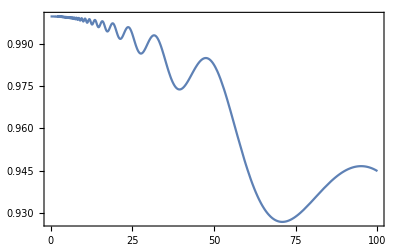

```mathematica
Plot[{Fav},{Ω,0,100},Frame->True]
```

```mathematica
(*now comupte fidelity of DDRF gate*)
```